# AMS-511 Foundations of Quantitative Finance

## Fall 2020 — Solutions 01

Robert J. Frey, Research Professor
Stony Brook University, Applied Mathematics and Statistics

Robert.Frey@StonyBrook.edu
http://www.ams.sunysb.edu/~frey

## Question 1

Suppose $1 was invested in 1776 at 3.3% interest compounded annually.

Approximately how much would that investment be worth today?

What if the interest rate were 6.6%?

### Solution

We will simplify the solution to assume the we invest at the end of 1776 and evaluate our balance at the end of 2017.

```mathematica
(1+0.033)^(2017-1776)
```

Alternately, we could have used TimeValue[ ] to compute the FV.

```mathematica
TimeValue[Cashflow[{1}],0.033,2017-1776]
```

At 6.6% …

```mathematica
(1+0.066)^(2017-1776)
```

Again, we could have used TimeValue[ ] to compute the FV.

```mathematica
TimeValue[Cashflow[{1}],0.066,2017-1776]
```

Note that the effect of interest rate on the FV is highly non-linear.

## Question 2

(Effective rates) Find the corresponding effective rates for:

3% compounded monthly,

18% compounded monthly,

18% compounded quarterly.

### Solution

Note that the effective rate r_eff for a nominal annual rate r compounded with frequency k is

r_eff=(1+r/k)^k-1

3% compounded monthly,

```mathematica
(1+0.03/12)^12-1
```

18% compounded monthly,

```mathematica
(1+0.18/12)^12-1
```

18% compounded quarterly.

```mathematica
(1+0.18/4)^4-1
```

## Question 3

Two copy machines are available. Both have useful lives of 5 years. One machine can be either leased or purchased outright, the other must be purchased. Below is a description of the three options with the first year’s maintenance included in the initial cost. There are then four additional yearly payments occurring at the beginning of each year, followed by the revenues from any resale. According to a PV analysis the least cost option is B:

| A | B | C
Initial outlay | 6000 | 30000 | 35000
Yearly expense | 8000 | 2000 | 1600
Resale value | 0 | 10000 | 12000
PV at 10% | 31559 | 30131 | 32621

It is not possible to compute an IRR on these options since the cashflows are all negative, except for the resale value. It is possible, however, to calculate the IRR on an incremental basis. Find the IRR on a change from A to B. Is this change justified on an IRR basis?

### Solution

We subtract from cash flow B the cash flow A. This produces the net cash flow freed up in moving from A to B.

```mathematica
vnCashFlowA={-6000,-8000,-8000,-8000,-8000,0};
vnCashFlowB={-30000,-2000,-2000,-2000,-2000,10000};
vnCashFlowAtoB=vnCashFlowB-vnCashFlowA
```

The resulting differential cash flow has an IRR of 11.8% which is favorable.

```mathematica
FindRoot[ TimeValue[Cashflow[vnCashFlowAtoB],r,0]==0,{r,.05}]
```

## Question 4

Gavin’s father, Mr. Jones, has just turned 90 years-old and is applying for a lifetime annuity that will pay $10,000 per year, starting 1 year from now, until he dies. He asks Gavin to analyze it for him. Gavin finds that according to statistical summaries, the probability of that Mr. Jones will die at a particular age is:

age | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101
prob. | 0.07 | 0.08 | 0.09 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.1 | 0.07 | 0.05 | 0.04

What would Gavin’s answers be to the following questions:

What is Mr. Jones’s (Gavin’s father’s) life expectancy?

What is the PV of an annuity at 8% interest that has a lifetime equal to Mr. Jones’s life expectancy? (For an annuity equal to a non-integral number of years use an averaging method.)

What is the expected PV of the annuity?

What is the standard deviation of the annuity?

### Solution

Note that the sum of the death probabilities sum to unity and will interpret this as a probability distribution. We will also make the simplification that if a person dies in his or her y^th year then the person’s age at death is on average y+1/2. We can now set up the following lists.

```mathematica
vnDeathAge=Range[90,101]+0.5
vnDeathProb={0.07,0.08,0.09,0.1,0.1,0.1,0.1,0.1,0.1,0.07,0.05,0.04}
Total[vnDeathProb]
```

What is Mr. Jones’s (Gavin’s father’s) life expectancy?

This is simply the inner product of probability and age.

```mathematica
vnDeathProb.vnDeathAge
```

What is the PV of an annuity at 8% interest that has a lifetime equal to Mr. Jones’s life expectancy? (For an annuity equal to a non-integral number of years use an averaging method.)

The TimeValue[ ] function handles partial periods, but any reasonable alternative weighting scheme is acceptable.

```mathematica
TimeValue[Annuity[b, n+0.5], i, 0]
```

```mathematica
TimeValue[Annuity[10000,5.63],0.08,0]
```

What is the expected PV of the annuity?

The length of the annuity is the death age minus 90. We can use Table[ ] to compute a list of PVs for each age. The expected value of the annuity is then the inner product of the death probabilities and the annuity values.

```mathematica
vnPV=Table[TimeValue[Annuity[10000,y],0.08,0],{y,vnDeathAge-90}]
```

```mathematica
vnDeathProb.vnPV
```

What is the standard deviation of the annuity?

The most straightforward way to calculate the standard deviation σ of a random variable X is

σ=√(E[X^2]-E[X]^2)

```mathematica
√(vnDeathProb.vnPV^2-(vnDeathProb.vnPV)^2)
```

## Question 5

The Smith family just took out a variable-rate mortgage on their new home. The mortgage value is $100,000, the term is 30 years, and the initial interest rate is 8%. This rate is guaranteed for 5 years, after which it will be adjusted to the prevailing rates. The mortgage will be adjusted by either modifying the payment amount or the length of the remaining loan.

In the text you are instructed to use yearly payment amounts, but for this assignment assume that the mortgage requires monthly payment,

What is the monthly payment at the start of the mortgage?

What is the mortgage balance after 5 years?

If the prevailing rate is 9% at the readjustment point and the mortgage termination date is kept constant, then what is the new monthly payment?

Under the same conditions immediately above, if the monthly payment is kept constant, then what it the new term (i.e., years and months remaining) of the mortgage?

### Solution

What is the monthly payment at the start of the mortgage?

```mathematica
nPmt=p/.FindRoot[100000==TimeValue[Annuity[p,30,1/12],EffectiveInterest[0.08,1/12],0],{p,100000 0.08/12}]
```

The initial monthly payment is $733.77.

What is the mortgage balance after 5 years?

```mathematica
nBalance=TimeValue[Annuity[nPmt,25,1/12],EffectiveInterest[0.08,1/12],0]
```

The balance remaining after 5 years is $95,069.86.

If the prevailing rate is 9% at the readjustment point and the mortgage termination date is kept constant, then what is the new monthly payment?

```mathematica
FindRoot[nBalance==TimeValue[Annuity[p,25,1/12],EffectiveInterest[0.09,1/12],0],{p,nBalance 0.09/12}]
```

The new monthly payment is $797.82.

Under the same conditions immediately above, if the monthly payment is kept constant, then what it the new term (i.e., years and months remaining) of the mortgage?

```mathematica
FindRoot[nBalance==TimeValue[Annuity[nPmt,n,1/12],EffectiveInterest[0.09,1/12],0],{n,25.}]
```

The term is extended to approximately an additional 39 years, 9 months, and 1 week.

## Question 6

A firm wishes to purchase a building for $10,000,000. Origination fees and other costs will total $25,000. The firm has $2,000,000 to cover the initial costs and down payment on the building. The mortgage terms available are a 5-year term with monthly payments computed at 7.5% with an amortization of 20 years.

What is the amount of the mortgage?

What are the monthly payments and final balloon payment?

How much interest did the firm pay over the 5 years of the mortgage?

### Solution

What is the amount of the mortgage?

The amount to be borrowed is the purchase price plus fees minus available funds.

```mathematica
nPV=(10000000+25000)-2000000
```

What are the monthly payments and final balloon payment?

Although the loan is for 5 years the payment is based on a 20 year amortization with the remaining balance at the end of 5 years due as a balloon payment.

```mathematica
nPmt=p/.FindRoot[nPV==TimeValue[Annuity[p,20,1/12],EffectiveInterest[0.075,1/12],0],{p,0.075nPV/12}]
```

```mathematica
nBal=TimeValue[Annuity[nPmt,15,1/12],EffectiveInterest[0.075,1/12],0]
```

How much interest did the firm pay over the 5 years of the mortgage?

The total amount paid less the decrease in principle owed is the total interest paid.

```mathematica
(5 12nPmt)-(nPV-nBal)
```

## Question 7

Arthur is planning on buying a house and needs to take out a mortgage for $200,000. He has two choices a 30-year with monthly payments of $1,468 and a 15-year with monthly payments of 1,854. Arthur wants to pay the lowest interest rate possible.

What is the interest rate on each mortgage and which mortgage should he pick?

He changes his mind and wants to pay the smallest amount of total interest. What are the total interest charges for each mortgage and which mortgage should he now pick?

### Solution

What is the interest rate on each mortgage and which mortgage should he pick?

```mathematica
nInt30=r/.FindRoot[200000==TimeValue[Annuity[1468,30,1/12],EffectiveInterest[r,1/12],0],{r,12 1468/20000}]
```

```mathematica
nInt15=r/.FindRoot[200000==TimeValue[Annuity[1854,15,1/12],EffectiveInterest[r,1/12],0],{r,12 1854/20000}]
```

The rate for the 15-year mortgage is about 0.5% lower.

He changes his mind and wants to pay the smallest amount of total interest. What are the total interest charges for each mortgage and which mortgage should he now pick?

```mathematica
30 12 1468-200000
```

```mathematica
15 12 1854-200000
```

The 15-year mortgage pays significantly lower interest over its term.

## Question 8

Meg has the opportunity to purchase bond A at origination for $98,930. The bond’s term is 10 years and pays semi-annual interest based on a nominal rate of 3.5%. She needs to invest the money for 5 years after which she wants to sell the bonds and put the funds towards the purchase of a house. She chose a 10-year bond to secure a higher interest rate.

What is bond A’s yield?

Another bond B is offered for sale with the same characteristics except the coupon rate is 3.75%. How would the market price bond B?

Meg is concerned that yields are at all time lows and is concerned that they will rise in the future. If the long term average yield for 5-year bonds is 4.75%, then how would the prices of bonds A and B be affected when Meg is ready to sell them?

### Solution

What is bond A’s yield?

We use FindRoot[ ] and FinancialBond[ ] to solve for the market yield for a 10-year bond of this quality.

```mathematica
nMarketYield=y/.FindRoot[FinancialBond[{"Coupon"->0.035,"FaceValue"->100000,"Maturity"->10,"CouponInterval"->1/2},{"InterestRate"->y,"Settlement"->0}]==98930,{y,.035}]
```

Another bond B is offered for sale with the same characteristics except the coupon rate is 3.75%. How would the market price bond B?

Bond B is has the same characteristics and can be expected to trade at the same yield. We apply FinancialBond[ ] with the same market yield.

```mathematica
FinancialBond[{"Coupon"->0.0375,"FaceValue"->100000,"Maturity"->10,"CouponInterval"->1/2},{"InterestRate"->nMarketYield,"Settlement"->0}]
```

Meg is concerned that yields are at all time lows and is concerned that they will rise in the future. If the long term average yield for 5-year bonds is 4.75%, then how would the prices of bonds A and B be affected when Meg is ready to sell them?

If in 5 years when she needs to sell the bonds with 5 years of their term remaining, then under the assumption that 5-year yields return to their long-term average, the 3.5% bond will lose $4,435.54 of its original value and the 3.75% bond will lose $5,415.43 of its original value. As expected, an increase in the market yield means a decrease in the price.

It is important to remember that the appropriate point on the yield curve to choose in pricing a bond is one that represents the remaining term of the bond and not its original term. Thus, a 10-year bond that has 5 years remaining is priced using the 5-year yield, not the 10-year.

```mathematica
FinancialBond[{"Coupon"->0.035,"FaceValue"->100000,"Maturity"->10,"CouponInterval"->1/2},{"InterestRate"->0.0475,"Settlement"->5}]-98930
```

```mathematica
FinancialBond[{"Coupon"->0.0375,"FaceValue"->100000,"Maturity"->10,"CouponInterval"->1/2},{"InterestRate"->0.0475,"Settlement"->5}]-101011
```

Note that the two computations below are equivalent; see the differences in “Maturity” and “Settlement”. This is because the cash flows in both cases are identical.

```mathematica
FinancialBond[{"Coupon"->0.035,"FaceValue"->100000,"Maturity"->10,"CouponInterval"->1/2},{"InterestRate"->0.0475,"Settlement"->5}]
```

```mathematica
FinancialBond[{"Coupon"->0.035,"FaceValue"->100000,"Maturity"->5,"CouponInterval"->1/2},{"InterestRate"->0.0475,"Settlement"->0}]
```

## Question 9

Ten years ago Sarah purchased her house and took out a mortgage for $150,000. The term of the mortgage was 30-years with monthly payments at an interest rate of 5.6%. She is selling the house and will use a portion of her proceeds to pay off the mortgage.

What is the principal balance on the mortgage that must be paid off?

How much total interest has been paid by Sarah over the past 10 years?

### Solution

First, we need to calculate the monthly payment for the mortgage.

```mathematica
nPmt=p/.FindRoot[150000==TimeValue[Annuity[p,30,1/12],EffectiveInterest[0.056,1/12],0],{p,100000 0.08/12}]
```

What is the principal balance on the mortgage that must be paid off?

After 10 years the mortgage would be equivalent to a 20 year mortgage with the given monthly payment at the mortgage's stated interest rate. Calculating the PV gives the balance.

```mathematica
nRemaining=TimeValue[Annuity[nPmt, 20, 1/12], EffectiveInterest[0.056, 1/12], 0]
```

How much total interest has been paid by Sarah over the past 10 years?

A straightforward way to calculate the interest paid is to take the total amount paid and subtract the decrease in principle. What is left is the interest paid.

```mathematica
10 12 nPmt-(150000-nRemaining)
```

## Question 10

Joe purchases a new car every 4 years, paying $25,000 (assume there is no inflation). He can put away money each month into a saving account which pays interest at the rate of 4% compounded monthly and needs to know what his monthly savings payment must be so that he has $25,000 in the account after 4 years. Alternately, he can fund the purchase price of $25,000 with a loan with a term of 4 years with monthly payments based on an interest rate of 6%.

How much must Joe save each month if he decides to save for the purchase of the car?

What is the monthly loan payment if Joe decides to borrow the money for the purchase of the car?

If Joe decides to save each month the same amount he would have had to pay for the loan, how much would he have left over when he purchased the car after 4 years of saving?

### Solution

How much must Joe save each month if he decides to save for the purchase of the car?

We must calculate the monthly amount to save that is required to achieve a FV of $25,000 given a 4% interest rate.

```mathematica
FindRoot[25000==TimeValue[Annuity[p,4,1/12],EffectiveInterest[0.04,1/12],4],{p,25000/(4 12)}]
```

What is the monthly loan payment if Joe decides to borrow the money for the purchase of the car?

In this case we must compute the monthly payments whose PV equal $25,000 given a 6% interest rate.

```mathematica
nPmt=p/.FindRoot[25000==TimeValue[Annuity[p,4,1/12],EffectiveInterest[0.06,1/12],0],{p,25000/(4 12)}]
```

If Joe decides to save each month the same amount he would have had to pay for the loan, how much would he have left over when he purchased the car after 4 years of saving?

Here we invest at 4% the same monthly amount as the loan would have required and then subtract the $25,000 cost of the car.

```mathematica
TimeValue[Annuity[nPmt,4,1/12],EffectiveInterest[0.04,1/12],4]-25000
```

Note that in this simplified example we have neglected the facts first, that inflation will affect the price of the car, and second, that we would have to pay income tax on the interest earned on savings. Also, there is the obvious point that using the savings approach we need 4 years to accumulate the funds to buy the car.

Nevertheless, the point is made that if Joe can manage to get ahead of things, perhaps using a cheaper car to cover the first 4 years, then he can structure his finances so either his monthly expenses can be reduced significantly or he can start a savings plan.

## Question 11

Consider two investments, both of which require an initial investment of $12,500. The first, A, pays a steady cashflow over the next 4 years. The second, B, pays a gradually increasing cashflow over the same period. These cash-flows are summarized in the table below:

| 0 | 1 | 2 | 3 | 4
A | -12500 | 4000 | 4000 | 4000 | 4000
B | -12500 |        0 | 2500 | 6000 | 8500

You need to make an investment decision. Assume annual compounding for your calculations.

An investment is viable if it has a positive IRR. You decide to pick the viable investment with the largest IRR, but if neither IRR is positive you will hold onto your $12,500.

Determine the viability of each investment in terms of its IRR.

What is your investment decision on an IRR basis: do not invest, invest in A, or invest in B?

Alternately, you have a threshold rate of return of 7% that you use to evaluate investment opportunities. An investment is considered viable if its PV is positive. You decide to pick the viable investment with the highest PV, but if neither is viable you will hold onto your $12,500.

Determine the viability of each investment in terms of its PV.

What is your investment decision on a PV basis: do not invest, invest in A, or invest in B?

### Solution

It is convenient to save the respective cash flows in the following lists.

```mathematica
vnCashFlowA={-12500,4000,4000,4000,4000};
vnCashFlowB={-12500,0,2500,6000,8000};
```

An investment is viable if it has a positive IRR. You decide to pick the viable investment with the largest IRR, but if neither IRR is positive you will hold onto your $12,500.

As the computation below shows A has a higher IRR at 10.7%.

```mathematica
FindRoot[0==TimeValue[Cashflow[vnCashFlowA],r,0],{r,0.05}]
FindRoot[0==TimeValue[Cashflow[vnCashFlowB],r,0],{r,0.05}]
```

Alternately, you have a threshold rate of return of 7% that you use to evaluate investment opportunities. An investment is considered viable if its PV is positive. You decide to pick the viable investment with the highest PV, but if neither is viable you will hold onto your $12,500.

Using a given rate of 7%, the PV of A is higher at $1,048.85.

```mathematica
TimeValue[Cashflow[vnCashFlowA],0.07,0]
TimeValue[Cashflow[vnCashFlowB],0.07,0]
```

## Question 12

Perform the following computations in Mathematica:

Plot (x^2 sin x) for x from -π to 2π.

Integrate (x^2 sin x) for x from -π to 2π.

Differentiate (x^2 sin x).

Write a function f[x] which, given x, computes (x^2 sin x).

Evaluate the function above for x from 0 to 1 in increments of 0.1

### Solution

Plot (x^2 sin x) for x from -π to 2π.

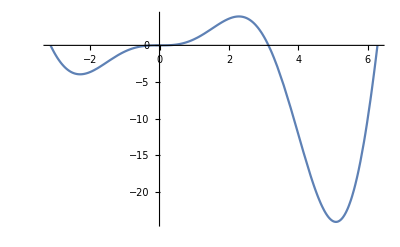

```mathematica
Plot[x^2 Sin[x],{x,-Pi,2 Pi}]
```

Integrate (x^2 sin x) for x from -π to 2π.

```mathematica
Integrate[x^2 Sin[x],{x,-Pi,2 Pi}]
```

4-5 π^2

Differentiate (x^2 sin x).

Note the x^2 can be entered as x, esc,ctl^, esc, 2, then hit the right arrow key to move the cursor to the baseline level.

```mathematica
D[x^2 Sin[x],x]
```

x^2 Cos[x]+2 x Sin[x]

Write a function f[x] which, given x, computes (x^2 sin x).

The three functions below are different ways of accomplishing the result.

```mathematica
f0[x_]:=x^2 Sin[x]
```

```mathematica
f1=#^2 Sin[#]&
```

#1^2 Sin[#1]&

```mathematica
f2=Function[{x},x^2 Sin[x]]
```

Function[{x},x^2 Sin[x]]

To demonstrate:

```mathematica
f0[θ]
f1[θ]
f2[θ]
```

θ^2 Sin[θ]

θ^2 Sin[θ]

θ^2 Sin[θ]

Reproducing the plot above:

```mathematica
Plot[f0[x],{x,-Pi,2 Pi}]
```

-Graphics-

Evaluate the function above for x from 0 to 1 in increments of 0.1

We'll demonstrate that all three functions produce the same result.

```mathematica
Table[f0[x],{x,0,1,0.1}]
Table[f1[x],{x,0,1,0.1}]
Table[f2[x],{x,0,1,0.1}]
```

{0.,0.000998334,0.00794677,0.0265968,0.0623069,0.119856,0.203271,0.315667,0.459108,0.634495,0.841471}

{0.,0.000998334,0.00794677,0.0265968,0.0623069,0.119856,0.203271,0.315667,0.459108,0.634495,0.841471}

{0.,0.000998334,0.00794677,0.0265968,0.0623069,0.119856,0.203271,0.315667,0.459108,0.634495,0.841471}

Extending this example further, to produce x,y-pairs suitable for plotting:

```mathematica
points=Table[{x,f1[x]},{x,0,1,0.1}]
```

{{0.,0.},{0.1,0.000998334},{0.2,0.00794677},{0.3,0.0265968},{0.4,0.0623069},{0.5,0.119856},{0.6,0.203271},{0.7,0.315667},{0.8,0.459108},{0.9,0.634495},{1.,0.841471}}

We can also overlay the smooth and discrete plots using Show[ ]:

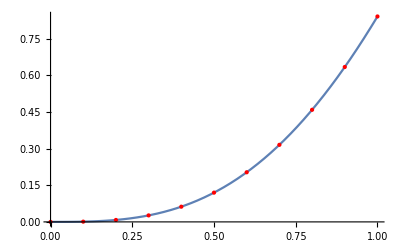

```mathematica
Show[
Plot[f1[x],{x,0,1}],
ListPlot[points,PlotStyle->{Red,PointSize[Large]}]
]
```